```mathematica
ClearAll["Global`*"]
```

## Te128

```mathematica
enData1={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData1={0.0005520853,0.0013638960,0.0031876746,0.0070482988,0.0147438968,0.0291781627,0.0546287641,0.0967615351,0.1621445680,0.2570520149,0.3855315460,0.5470434358,0.7343651418,0.9326987533,1.1208084653,1.2744577653,1.3715480845,1.3975433970,1.3494226282,1.2367769391,1.0796528592,0.9039030721,0.7356193365,0.5963542225,0.5003105763,0.4538085194,0.4565388572,0.5036697982,0.5878696567,0.7006432914,0.8328699409,0.9748774613,1.1166215387,1.2484496667,1.3625277806,1.4544625993,1.5242633151,1.5758398050,1.6148183705,1.6453432336,1.6672517803,1.6751008782,1.6598202059,1.6125612881,1.5292027129,1.4135524898,1.2777909883,1.1398680746,1.0188207314,0.9297320139,0.8800322348,0.8681711705,0.8847560886,0.9154724664,0.9447323851,0.9590497396,0.9494737788,0.9128224901,0.8517874206,0.7741594358,0.6914569913,0.6171786902,0.5648197243,0.5457501598,0.5670930444,0.6298651424,0.7278013392,0.8473689468,0.9693665982,1.0721304712,1.1358117157,1.1466661963,1.1000917339,1.0014349904,0.8643099846,0.7070269164,0.5483409160,0.4038358931,0.2838570818,0.1932321628,0.1323972842,0.0992090906,0.0907393304,0.1046186370,0.1398497389,0.1972850497,0.2800514120,0.3940688198,0.5484949146,0.7555693133,1.0291434044,1.3813755625,1.8177351082,2.3314302904,2.8992353975,3.4809152397,4.0236896531,4.4715515815,4.7773583969,4.9143246895,4.8835287601,4.7153763667,4.4650203222,4.2035108234,4.0071364181,3.9468704334,4.0786818036,4.4346812316,5.0153302645,5.7841087865,6.6671780017,7.5605273728,8.3452844881,8.9088338473,9.1665920509,9.0782726491,8.6539393090,7.9484997748,7.0470166449,6.0457346358,5.0342254363,4.0827136402,3.2363449762,2.5158959574,1.9229015517,1.4466414959,1.0707503013,0.7780638382,0.5532918161,0.3838782883,0.2597964124,0.1730118856,0.1170761416,0.0869656193,0.0790244137,0.0907705755,0.1203883888,0.1658976309,0.2241916244,0.2902874632,0.3571595722,0.4163896473,0.4595849373,0.4801938819,0.4751307619,0.4456296334,0.3970012758,0.3373595823,0.2757377727,0.2201777694,0.1763023032,0.1466416555,0.1307184719,0.1257053778,0.1273982676,0.1312628882,0.1333609912,0.1310128642,0.1231057333,0.1100255761,0.0932730776,0.0748997296,0.0569354438,0.0409569695,0.0278772806,0.0179522659,0.0109375352,0.0063044009,0.0034378659,0.0017735897,0.0008656367,0.0003997019,0.0001746041,0.0000721590,0.0000282127,0.0000104355,0.0000036518,0.0000012090,0.0000003786,0.0000001122,0.0000000315,0.0000000083,0.0000000021,0.0000000005,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enData2={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData2={0.0000000160,0.0000000388,0.0000000892,0.0000001948,0.0000004046,0.0000007999,0.0000015075,0.0000027122,0.0000046659,0.0000076901,0.0000121676,0.0000185238,0.0000271981,0.0000386086,0.0000531142,0.0000709791,0.0000923434,0.0001172079,0.0001454424,0.0001768263,0.0002111264,0.0002482014,0.0002881065,0.0003311638,0.0003779717,0.0004293527,0.0004862630,0.0005496871,0.0006205024,0.0006992378,0.0007856284,0.0008779419,0.0009722312,0.0010618865,0.0011379533,0.0011905357,0.0012111928,0.0011957093,0.0011462743,0.0010721324,0.0009882516,0.0009122589,0.0008605293,0.0008445747,0.0008687038,0.0009294267,0.0010165199,0.0011152579,0.0012091727,0.0012827742,0.0013238428,0.0013250827,0.0012850142,0.0012080270,0.0011035465,0.0009843671,0.0008643740,0.0007560671,0.0006684143,0.0006055291,0.0005664629,0.0005461055,0.0005368856,0.0005307730,0.0005210497,0.0005034437,0.0004764545,0.0004409560,0.0003993565,0.0003546631,0.0003097377,0.0002668911,0.0002278108,0.0001937216,0.0001656508,0.0001446927,0.0001322137,0.0001299882,0.0001402913,0.0001659887,0.0002106394,0.0002785387,0.0003745085,0.0005031609,0.0006674273,0.0008664323,0.0010932562,0.0013335542,0.0015661035,0.0017659031,0.0019095045,0.0019811633,0.0019777057,0.0019101458,0.0018011179,0.0016787210,0.0015687506,0.0014879034,0.0014401475,0.0014172349,0.0014028407,0.0013786175,0.0013300010,0.0012499676,0.0011399046,0.0010078659,0.0008653045,0.0007236492,0.0005918078,0.0004750870,0.0003753999,0.0002922509,0.0002239061,0.0001683186,0.0001236342,0.0000883226,0.0000610930,0.0000407564,0.0000261390,0.0000160762,0.0000094639,0.0000053257,0.0000028622,0.0000014682,0.0000007186,0.0000003356,0.0000001495,0.0000000635,0.0000000258,0.0000000100,0.0000000037,0.0000000013,0.0000000004,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Xe128

```mathematica
enData3={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData3={0.0000449782,0.0001111272,0.0002597586,0.0005744552,0.0012019471,0.0023793923,0.0044566632,0.0078982756,0.0132450862,0.0210187364,0.0315666391,0.0448721766,0.0603857859,0.0769521303,0.0928996972,0.1063145955,0.1154511708,0.1191671778,0.1172441190,0.1104827253,0.1005402579,0.0895663701,0.0797573601,0.0729601813,0.0704199798,0.0727021572,0.0797613282,0.0910950621,0.1059155579,0.1232920667,0.1422500296,0.1618455703,0.1812505012,0.1998707269,0.2174795649,0.2342965246,0.2509169332,0.2680310179,0.2859669966,0.3042132786,0.3211515341,0.3342035118,0.3404477843,0.3375537069,0.3247099161,0.3031857527,0.2762850475,0.2486797386,0.2253398679,0.2104059488,0.2063348024,0.2135168392,0.2303843568,0.2538843426,0.2801230401,0.3050077561,0.3247834597,0.3364412215,0.3380220068,0.3288359127,0.3095774740,0.2822785066,0.2500382912,0.2165211576,0.1852949274,0.1591587946,0.1396363934,0.1267729736,0.1192884406,0.1150338015,0.1116134919,0.1069962444,0.0999525706,0.0902205038,0.0783909870,0.0655894240,0.0530814104,0.0419331249,0.0328149845,0.0259726760,0.0213301149,0.0186550618,0.0177169216,0.0183910309,0.0206998238,0.0248125063,0.0310385850,0.0398409744,0.0518648644,0.0679423919,0.0890108791,0.1158934306,0.1489422483,0.1876230492,0.2301888322,0.2736115259,0.3138849088,0.3466902659,0.3682732227,0.3762801303,0.3702956057,0.3519182153,0.3243693709,0.2917827094,0.2584046164,0.2279243710,0.2030638043,0.1854414929,0.1756378013,0.1733540592,0.1775798173,0.1867318515,0.1987775235,0.2113821720,0.2221178894,0.2287431934,0.2295214136,0.2235072060,0.2107145174,0.1920988960,0.1693406452,0.1444827726,0.1195282238,0.0961098930,0.0753106795,0.0576489210,0.0431874812,0.0316965279,0.0228061583,0.0161134270,0.0112397321,0.0078541071,0.0056814865,0.0045072908,0.0041791239,0.0045997698,0.0057057415,0.0074313904,0.0096667584,0.0122238810,0.0148274822,0.0171400621,0.0188194023,0.0195929300,0.0193244132,0.0180490460,0.0159637725,0.0133761892,0.0106300541,0.0080318977,0.0057994758,0.0040419065,0.0027691462,0.0019201847,0.0013971130,0.0010949594,0.0009220827,0.0008103632,0.0007171263,0.0006216736,0.0005191456,0.0004138456,0.0003134804,0.0002251233,0.0001531054,0.0000985577,0.0000600358,0.0000346016,0.0000188678,0.0000097337,0.0000047507,0.0000021936,0.0000009582,0.0000003960,0.0000001548,0.0000000573,0.0000000200,0.0000000066,0.0000000021,0.0000000006,0.0000000002,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Numerical params

```mathematica
xdp=1.56;
chi12=0.8;
el1="^128Te";
el2="^128Xe";
```

## Figures

### Figure1

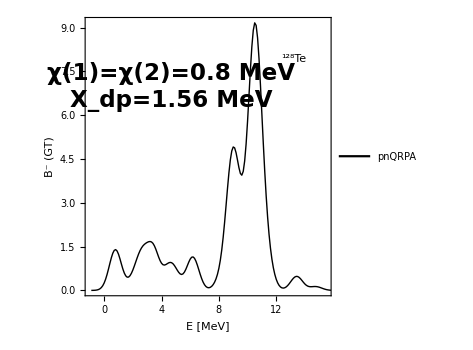

```mathematica
tableFig1=Table[{enData1[[i]],strData1[[i]]},{i,1,Length[strData1]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,15.5},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[StringTemplate["``"][el1],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.85,0.85}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_6/new_figs/fig1_set6.pdf",Show[fig1],ImageResolution->1200];
```

### Figure2

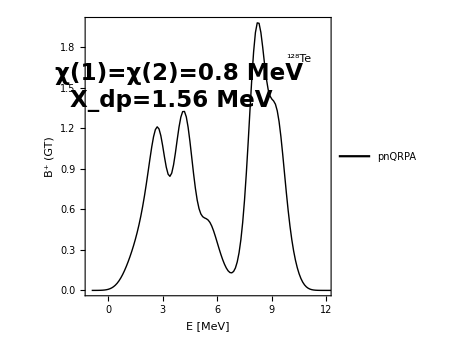

```mathematica
tableFig2=Table[{enData2[[i]],strData2[[i]]*1000},{i,1,Length[strData2]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,12},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.38,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[StringTemplate["``"][el1],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.87,0.85}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_6/new_figs/fig2_set6.pdf",Show[fig2],ImageResolution->1200];
```

### Figure3

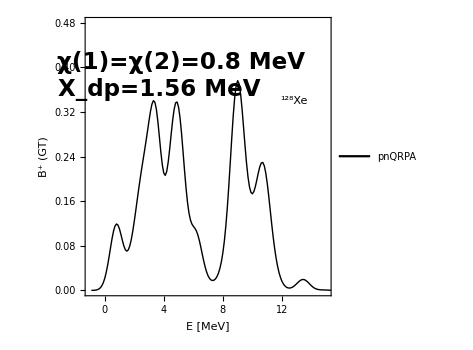

```mathematica
tableFig3=Table[{enData3[[i]],strData3[[i]]},{i,1,Length[strData3]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,15},{0,0.48}},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.25,0.93}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.39,0.84}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.3,0.74}]],Inset[Framed[Style[StringTemplate["``"][el2],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.85,0.7}]]}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_6/new_figs/fig3_set6.pdf",Show[fig3],ImageResolution->1200];
```